### Get all fixed points x* for dx/dt = rx+4x^3-9x^5

```mathematica
Solve[r*x + 4*x^3 -9*x^5==0,x]
```

{{x→0},{x→-1/3 √(2-√(4+9 r))},{x→1/3 √(2-√(4+9 r))},{x→-1/3 √(2+√(4+9 r))},{x→1/3 √(2+√(4+9 r))}}

### Bifurcation diagram of x* vs r

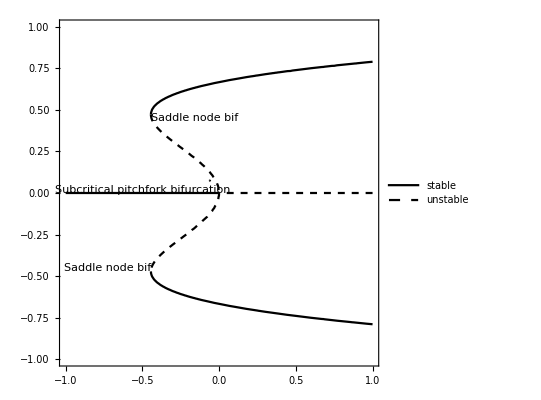

```mathematica
f[x_]:=r*x + 4*x^3 -9*x^5;
derivOfx= D[f[x],x];
conplot = ContourPlot[{
ConditionalExpression[f[x],derivOfx<0] == 0,
ConditionalExpression[f[x],derivOfx>0] == 0},
{r, -1, 1},{x,-1,1},ContourStyle -> {{Black},{Black,Dashed}},
PlotLegends->{"stable", "unstable"}];


align[Right]={1,0};
align[Center]={0,0};        
align[Left]={-1,0};

lText=Text["Saddle node bif",{-4/9,0.45},align[Left]];
cText=Text["Subcritical pitchfork bifurcation",{-0.5,0.02},align[Center]];
rText=Text["Saddle node bif",{-4/9,-0.45},align[Right]];

txt=Graphics[{lText,cText,rText}];





Show[conplot,txt]
```

#### Find r critical

```mathematica
Clear[x];
f[x_]:=r*x + 4*x^3 - 9*x^5;
dx = D[f[x],x];
Solve[dx == 0,x]
```

{{x→-(√(2-√(4+5 r)))/(√15)},{x→(√(2-√(4+5 r)))/(√15)},{x→-(√(2+√(4+5 r)))/(√15)},{x→(√(2+√(4+5 r)))/(√15)}}

```mathematica
x1 = -Sqrt[2-Sqrt[4+5*r]]/Sqrt[15];
x2 = Sqrt[2-Sqrt[4+5*r]]/Sqrt[15];
x3 = -Sqrt[2+Sqrt[4+5*r]]/Sqrt[15];
x4= Sqrt[2+Sqrt[4+5*r]]/Sqrt[15];
Solve[f[x1]==0,r]
Solve[f[x2]==0,r]
Solve[f[x3]==0,r]
Solve[f[x4]==0,r]
```

{{r→0}}

{{r→0}}

{{r→-4/9}}

{{r→-4/9}}